## Syntax Reminders

Evaluate expressions by selecting the cell bracket or positioning the mouse anywhere within an expression, and hit ⇧-⏎ on the keyboard or ⌤  on the numpad.

The symbol % denotes the previous output.

For numerical expressions:  exact input ⟹ exact output,  approx input ⟹ approx output

Entering Two-Dimensional Expressions can be done with the Basic Math Assistant palette or with keyboard shortcuts

2D expression | 1D input | Keyboard entry
x^m | x^m | xCtrl[^] m
x/y | x/y | x Ctrl[/] y
x_i | x_i | x Ctrl[_] i

### Getting Help

The Documentation Center, under the Help menu, gives you access to Mathematica’s on-line documentation. An overview of Mathematica is presented in the First Five Minutes with Mathematica section.

Long function names can be difficult to enter and remember,  Complete Selection Ctrl[k] and Make Template Ctrl[K] under the Edit Menu increases the speed, correctness, and convenience of Notebooks.

Alternatively one can use a Palette such as the Basic Math Assistant.

### Replacement Rules

Solutions to equations are returned as a list of lists of replacement rules:

```mathematica
sol=Solve[{a x^2+b y==0,c x+d y==0},{x,y}]
```

{{y→0,x→0},{y→-(b c^2)/(a d^2),x→(b c)/(a d)}}

To use the solutions, the ReplaceAll (/.) command is used. Here we substitute both solutions into both equations:

```mathematica
{a x^2+b y==0,c x+d y==0}/.sol
```

(True | True
True | True)

Substitute the second (or Last) solution into the variable x:

```mathematica
x/.sol⟦2⟧
```

(b c)/(a d)

Remove this definition:

```mathematica
Remove[sol]
```

### Protected Symbols

Certain symbols, such as D (which denotes the partial derivative) are protected:

```mathematica
D=2
```

Set::wrsym: Symbol D is Protected.

2

If one uses lower-case letters this problem is avoided.

An alternative is to use, say, script letters, available in the SpecialCharacters palette:

```mathematica
𝒟=2
```

2

Note that most special characters have Esc aliases (or keyboard shortcuts):  eg  𝒟 ← EscscDEsc,  while  𝔻 ← EscdsDEsc  etc…

### Basic List Operations

One can extract parts of an expression expr using Part or using the shorthand form expr[[n]] or expr⟦n⟧, with ⟦ ← Esc[[Esc :

```mathematica
{x,y,z}⟦2⟧
```

2

One can extract multiple entries using a list of indices:

```mathematica
{x,y,z}⟦{2,3,2,1}⟧
```

{y,z,y,x}

A matrix is a list of lists (rows).

Here is the first row of the matrix (a | b
c | d)={{a,b},{c,d}} :

```mathematica
({{a, b}, {c, d}})⟦1⟧
```

{a,b}

Here is the (2,1) element:

```mathematica
({{a, b}, {c, d}})⟦2,1⟧
```

Swap the first and second rows:

```mathematica
({{a, b}, {c, d}})⟦{2,1}⟧
```

The easiest way of swapping columns is to take the Transpose of the matrix first.

### Generating Matrices

One can construct matrices in a variety of ways. For now, we will do it either:

by hand, typing in a list of lists;

using the Basic Math Assistant palette;

using Insert ▸ Table/Matrix ▸ New…  ;

or using the Table command.

Construct a 2×3 matrix as a list of lists:

```mathematica
{{a,b,c},{d,e,f}}
```

(a | b | c
d | e | f)

Use Table to construct a general 4×6 matrix:

```mathematica
Table[Subscript[a, i,j],{i,4},{j,6}]
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5) | a_(1,6)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5) | a_(2,6)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5) | a_(3,6)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5) | a_(4,6))

If you are not using TraditionalForm for output, you can use MatrixForm to display matrices:

```mathematica
MatrixForm@%
```

### Defining Functions

Define the function, f(x)=x^2+1:

```mathematica
f[x_]:=x^2+1
```

Note that the symbol f went from blue = undefined to black = defined.

Here is f(2):

```mathematica
f[2]
```

5

Here is f({x,y}):

```mathematica
f[{x,y}]
```

{x^2+1,y^2+1}

To see what definitions are associated with a symbol, use ?

```mathematica
?f
```

Global`f

f[x_]:=x^2+1

Clear this definition:

```mathematica
Clear[f]
```

The symbol f has now returned to being blue:

```mathematica
?f
```

Global`f

### Defining Vector Functions

Define g(x,y)=(x y,x^2-y^2), a vector function (or map) g:ℝ^2→ℝ^2:

```mathematica
g[{x_,y_}]:={x y,x^2-y^2}
```

Compute g(a,b):

```mathematica
g[{a,b}]
```

{a b,a^2-b^2}

Note that g takes a vector and returns a vector. This is useful when composing such functions.

Compute g∘g(x,y):

```mathematica
g@g[{x,y}]//Simplify
```

{x y (x^2-y^2),-x^4+3 x^2 y^2-y^4}

Remove this definition:

```mathematica
Clear[g]
```

## One Variable

### Taylor series

The easiest way to compute the tangent line (or linear approximation) to a function f(x) at a point a is to observe that it is just the Taylor series of f(x) about a to first order.

Compute  the Taylor series of f(x) about a to first order:

```mathematica
f[x]+O[x,a]^2
```

f(a)+(x-a) f'(a)+O((x-a)^2)

Alternatively, use Series:

```mathematica
Series[f[x],{x,a,1}]
```

f(a)+(x-a) f'(a)+O((x-a)^2)

Plot f(x)=tan(sin(x))-sin(tan(x)) over 0≤x≤π. Compute the Taylor series (using Series) of f(x) about x=0 and x=π. Relate the Taylor series to the features of the plot. What happens at x=π/2? [5 Marks]

Solution

Define the function f(x)=tan(sin(x))-sin(tan(x)):

```mathematica
f(x_):=tan(sin(x))-sin(tan(x))
```

Plot f(x) over 0≤x≤π:

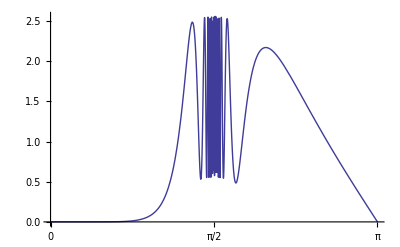

```mathematica
Plot[f(x),{x,0,π},Ticks->{{0,π/2,π},Automatic}]
```

f(x) is very flat near x=0 which is consistent with the result that the Maclaurin series starts at x^7.

```mathematica
Series[f(x),{x,0,10}]
```

x^7/30+(29 x^9)/756+O(x^11)

f(x) is linear near x=π with slope -2 which is consistent with the first term in the Taylor series about π.

```mathematica
Series[f(x),{x,π,4}]
```

-2 (x-π)-1/3 (x-π)^3+O((x-π)^5)

The point x=π/2 is an essential singularity and the Taylor series does not exist at this point. Limit returns Interval objects to represent ranges of possible values at essential singularities:

```mathematica
lim_(x->π/2) f(x)
```

Interval[{tan(1)-1,1+tan(1)}]

```mathematica
N[%]
```

Interval[{0.557408,2.55741}]

Show all these features together:

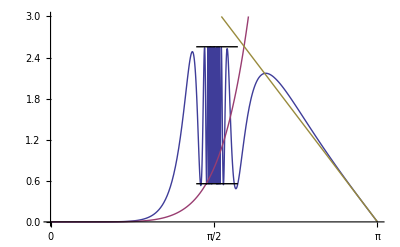

```mathematica
Plot[{Tooltip[f(x)],Tooltip[x^7/30],Tooltip[-2 (x-π)]},{x,0,π},PlotPoints->200,PlotRange->{0,3},Ticks->{{0,π/2,π},Automatic},Epilog->{Tooltip[Line[({{1.4, tan(1)-1}, {1.8, tan(1)-1}})],"lower"],Tooltip[Line[({{1.4, 1+tan(1)}, {1.8, 1+tan(1)}})],"upper"]}]
```

### Maxima and Minima

Construct a polynomial g(x) with the following properties:

Require that g(0)==3/2, g'(0)==-4 and g'(x)==0 at x=-1,1,2,4. Hint: g'(x)=α (x-β)(x-γ)⋯(x-δ) vanishes at β, γ,…, δ. Integrate to find g(x). You need to determine α and the constant of integration. [3 Marks]

Over a suitable range, plot g(x) and g'(x) together, so that you can the see the zeros, maxima, minima, inflection point(s), and its tangent line (see above) at x==1. [3 Marks]

Compute the zeros, maxima, minima, and inflection points of g(x). Display these on your plot of g(x) and g'(x). [3 Marks]

Recall that an inflection point is where the second derivative vanishes; it's not necessarily a critical point.

Solution

Require that g'(0)==-4 and g'(x)==0 at x=-1,1,2,4:

```mathematica
Clear[g]
```

```mathematica
g'(x_):=α (x+1) (x-1)(x-2)(x-4)
```

```mathematica
Solve[g'(0)==-4]
```

{{α→1/2}}

Require that g(0)==3/2:

```mathematica
g(x_)=∫g'(x)ⅆx+c/.First[%]
```

c+x^5/10-(3 x^4)/4+(7 x^3)/6+(3 x^2)/2-4 x

```mathematica
Solve[g(0)==3/2]
```

{{c→3/2}}

```mathematica
g(x_)=g(x)/.First[%]
```

x^5/10-(3 x^4)/4+(7 x^3)/6+(3 x^2)/2-4 x+3/2

Use Taylor series to obtain the tangent line at x=1:

```mathematica
g(x)+O[x,1]^2
```

-29/60+O((x-1)^2)

```mathematica
g(1)
```

-29/60

Plot g(x) and g'(x) together. One can see the zeros, maxima, minima, inflection points, and tangent line at x==1:

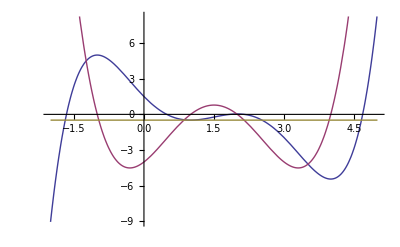

```mathematica
Plot[{Tooltip[g[x],"g"],Tooltip[g'[x],"g'"],Tooltip[g[1],"tangent"]},{x,-2,5}]
```

Compute the zeros. The 5 zeros are roots of a quintic and cannot be expressed as radicals:

```mathematica
zeros=Solve[g(x)==0]
```

{{x→Root[6 #1^5-45 #1^4+70 #1^3+90 #1^2-240 #1+90&,1]},{x→Root[6 #1^5-45 #1^4+70 #1^3+90 #1^2-240 #1+90&,2]},{x→Root[6 #1^5-45 #1^4+70 #1^3+90 #1^2-240 #1+90&,3]},{x→Root[6 #1^5-45 #1^4+70 #1^3+90 #1^2-240 #1+90&,4]},{x→Root[6 #1^5-45 #1^4+70 #1^3+90 #1^2-240 #1+90&,5]}}

The numerical values agree with the plot:

```mathematica
N[zeros]
```

{{x→-1.65897},{x→0.488511},{x→1.84367},{x→2.1437},{x→4.68308}}

Note that you can Factor the (numerical value of the) polynomial, which clearly displays the real roots:

```mathematica
Factor[N[10g(x)]]
```

(1. x-4.68308) (1. x-2.1437) (1. x-1.84367) (1. x-0.488511) (1. x+1.65897)

To compute the maxima and minima, and inflection points we need to compute the derivative (which we already know from the construction of g(x)). Determine the critical points:

```mathematica
critical=Solve[g'(x)==0]
```

{{x→-1},{x→1},{x→2},{x→4}}

Observe that the Taylor polynomial has no linear term at critical points and is quadratic in the neighbourhood of these points:

```mathematica
g(t)+O[t,x]^3/.critical
```

{299/30-15 (t+1)^2+O((t+1)^3),-29/30+3 (t-1)^2+O((t-1)^3),1/15-3 (t-2)^2+O((t-2)^3),-163/15+15 (t-4)^2+O((t-4)^3)}

Apply the second derivative test:

```mathematica
{x,g''(x)<0,g''(x)==0,g''(x)>0}/.critical
```

(-1 | True | False | False
1 | False | False | True
2 | True | False | False
4 | False | False | True)

Hence x=-1 and x=2 are local maxima and x=1 and x=4 are local minima.

To obtain the inflection points we need to compute the second derivative:

```mathematica
inflections=Solve[g''(x)==0]
```

{{x→3/2},{x→1/2 (3-√13)},{x→1/2 (3+√13)}}

Observe that the Taylor series has no quadratic term at inflection points:

```mathematica
g(x)+O[x,3/2]^4
```

-9/40+25/32 (x-3/2)-13/12 (x-3/2)^3+O((x-3/2)^4)

Show the zeros in Blue, the critical points in Red, and the inflection points in Green:

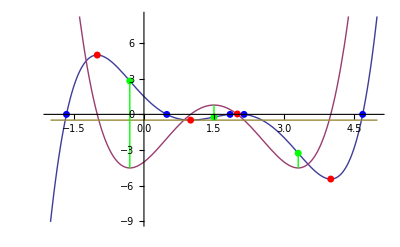

```mathematica
Plot[{Tooltip[g[x],"g"],Tooltip[g'[x],"g'"],Tooltip[g[1],"tangent"]},{x,-2,5},Epilog->{AbsolutePointSize[5],Blue,Tooltip[Point[{x,g[x]}]/.zeros,"zero"],Red,Tooltip[Point[{x,g[x]}]/.critical,"critical point"],Green,Tooltip[Point[{x,g[x]}]/.inflections,"inflection"],Line[{{x,g'[x]},{x,g[x]}}]/.inflections}]
```

The following code, which you need to enter, plots an Argand diagram of the complex roots of g(x)==c (in blue), along with points where g'(x)==0 (in red).

```mathematica
ArgandPlot[g_,c_,opts___]:=
Module[{z},
ListPlot[Evaluate[
{
{Re[z],Im[z]}/.NSolve[g[z]==c,z],
{Re[z],Im[z]}/.NSolve[g'[z]==0,z]
}
],
opts,PlotStyle->AbsolutePointSize[5],
PlotRange->{{-2,5},{-1.2,1.2}}]
]
```

For the function g(x), constructed in the previous exercise, produce an Argand diagram of the complex roots of g(x)==c using Manipulate to vary c. Describe what you see. What happens when roots coalesce? Where do  the roots coalesce? [3 Marks]

Answer:

```mathematica
Manipulate[ArgandPlot[g,c,ImageSize->500],{{c,0},-20,15},SaveDefinitions->True]
```

When two real roots coalesce, they move off into the complex plane. When two complex roots coalesce, they move apart along the real axis. This coalescence happens when g(x)==g'(x)==0, that is where the function and its derivative are both zero.

Here is a visualization that shows the Argand diagram alongside a plot of g(x)==c and g'(x):

```mathematica
Manipulate[Module[{z},
GraphicsRow[{ArgandPlot[g,c],Plot[{g[x]==c,g'[x]},{x,-2,5},PlotRange->{-30,30}]},ImageSize->800]],{{c,0},-20,15},SaveDefinitions->True]
```

## Many Variables

The multidimensional Taylor series is

f(x+δx)==f(x)+δx·∇f(x)+1/(2!)(δx·∇)^2 f(x)+O(δx^3)

The directional derivative is

f'_(û)(x)==lim_(ϵ→0) (f(x+ϵ û)-f(x))/ϵ==û·∇f(x)

Why is the gradient always perpendicular to contour lines (or, in 3D, contour surfaces)? 
Hint: Think about the value of f_(û)' on a contour. [2 Marks]

Answer

Moving along a contour line in the direction û, the value of the function is constant so f_(û)'==0==∇f·û. A dot product a·b between two (non-zero) vectors a and b vanishes when a is perpendicular to b. Hence ∇f⊥û.

A standard problem in calculus:

A closed rectangular container of volume  α m^3 needs to be constructed out of the minimum amount of material. Let the side lengths be x and y and the height be z. Then V=xyz=α>0  and A=2xy+2zx+2yz, where x>0, y>0, and z>0.

Find the area A=A(x,y), its gradient ∇A(x,y), and the Jacobian ∇(∇A(x,y)), as functions of x and y. [2 Marks]

Find and classify the critical points of A(x,y). What is the surface area (and volume) of the container at the critical points? [2 Marks]

For α=1 plot A(x,y) for x and y in (0.1,5) [1 Mark]

For α=1 find the equation for the tangent plane and normal to A(x,y) at an arbitrary point (a,b). [2 Marks]

Make a combined plot of A(x,y) for x,y∈(0.1,3) and an Arrow pointing in the negative normal direction at some point (a,b). Optionally, make it dynamic using Manipulate. [1 Marks]

Solution

Define the volume:

```mathematica
V[x_,y_,z_]:=x y z
```

Determine the height z as function of x and y:

```mathematica
Solve[V[x,y,z]==α,z]
```

{{z→α/(x y)}}

Define the surface area as a function of x and y and the fixed volume α:

```mathematica
Subscript[A, α_][x_,y_]=2x y+2z x+2y z/.z->α/(x y)
```

(2 α)/x+2 x y+(2 α)/y

Define the (two-dimensional) gradient operator using Del (∇):

```mathematica
∇f_:={D[f, x],D[f, y]}
```

Compute the gradient:

```mathematica
∇Subscript[A, α](x,y)
```

{2 y-(2 α)/x^2,2 x-(2 α)/y^2}

Compute the Hessian:

```mathematica
∇(∇Subscript[A, α](x,y))
```

((4 α)/x^3 | 2
2 | (4 α)/y^3)

One can use Solve to determine the critical points:

```mathematica
Solve[∇Subscript[A, α](x,y)=={0,0},{x,y}]
```

{{x→α^(1/3),y→α^(1/3)},{x→--1^(1/3) α^(1/3),y→--1^(1/3) α^(1/3)},{x→(-1)^(2/3) α^(1/3),y→(-1)^(2/3) α^(1/3)}}

Select the real solution:

```mathematica
critical=First[%]
```

{x→α^(1/3),y→α^(1/3)}

Compute the Hessian for the critical point:

```mathematica
∇(∇Subscript[A, α](x,y))/.critical
```

(4 | 2
2 | 4)

The determinant (or using the Eigenvalues) tells us that this point is a local minimum:

```mathematica
Det[%]
```

12

```mathematica
Eigenvalues[%%]
```

{6,2}

Obtain the surface area:

```mathematica
Subscript[A, α](x,y)/.critical
```

6 α^(2/3)

The volume is fixed; V==α.

Here is a plot of A_1(x,y) for x and y in (0.1,5):

```mathematica
Plot3D[Subscript[A, 1](x,y),{x,0.1,5},{y,0.1,5},PlotRange->{4,12},Mesh->False,AxesLabel->{x,y},BoxRatios->Automatic,PlotStyle->Opacity[0.5]]
```

-Graphics3D-

The constant and linear terms in the Taylor series gives us the equation of the tangent plane:

```mathematica
Series[Subscript[A, 1](x,y),{x,a,1},{y,b,1}]
```

((2 a b+2/a+2/b)+(2 a-2/b^2) (y-b)+O((y-b)^2))+(x-a) ((2 b-2/a^2)+2 (y-b)+O((y-b)^2))+O((x-a)^2)

Here is the tangent plane for α=1 at an arbitrary point (a,b):

```mathematica
tangent[{a_,b_}][{x_,y_}]=Subscript[A, 1](a,b)+{x-a,y-b}.(∇Subscript[A, 1](x,y)/.{x->a,y->b})
```

(2 b-2/a^2) (x-a)+(2 a-2/b^2) (y-b)+2 a b+2/a+2/b

```mathematica
tangentplane[{a_,b_}]:=Plot3D[Evaluate@tangent[{a,b}][{x,y}],{x,a-0.1,a+0.1},{y,b-0.1,b+0.1},Mesh->False,RegionFunction->({x,y}↦(x-a)^2+(y-b)^2≤0.01)]
```

For z==f(x,y) we have f(x,y)-z==0⟹{∂_x,∂_y,∂_z}(f(x,y)-z)=={f^(1,0)(x,y),f^(0,1)(x,y),-1}.

The normal to A_1(x,y) at an arbitrary point (a,b) is (n_x,n_y,n_z)∝(A_1^(1,0)(a,b),A_1^(0,1)(a,b),-1):

```mathematica
normal[{a_,b_}]:=Arrow[{{a,b,Subscript[A, 1](a,b)},{a,b,Subscript[A, 1](a,b)}-Normalize[Join[∇Subscript[A, 1](x,y),{-1}]]}]/.{x->a,y->b}
```

Here is combined plot of A_1(x,y) with an Arrow pointing in the negative normal direction at some point (a,b) made dynamic using Manipulate:

```mathematica
Manipulate[Show[Plot3D[Subscript[A, 1](x,y),{x,0.1,3},{y,0.1,3},Mesh->False,AxesLabel->{x,y},BoxRatios->1,PlotStyle->Opacity[0.5],PlotRange->{6,9},PlotPoints->30],tangentplane[pt],Graphics3D[normal[pt]]],{pt,{0.6,0.6},{4,4}},SaveDefinitions->True]
```

## Vector Operators

The standard vector calculus identities are given in the lecture notes:

𝒶.(𝒷×𝒸)==𝒷.(𝒸×𝒶)==𝒸.(𝒶×𝒷)

𝒶×(𝒷×𝒸)==𝒷 (𝒶.𝒸)-𝒸 (𝒶.𝒷)

▽(𝒻 ℊ)==𝒻 (▽(ℊ))+ℊ (▽(𝒻))

▽(𝒶.𝒷)==𝒶×(▽×𝒷)+𝒷×(▽×𝒶)+𝒶.▽(𝒷)+𝒷.▽(𝒶)

▽·(𝒻 𝒶)==𝒻 (▽·𝒶)+𝒶.(▽(𝒻))

▽·(𝒶×𝒷)==𝒷.(▽×𝒶)-𝒶.(▽×𝒷)

▽×▽(𝒻)==0

▽·(▽×𝒶)==0

Here is one way to implement vector operators:

```mathematica
▽/:▽[f_]:={D[f, x],D[f, y],D[f, z]}
```

```mathematica
▽/:▽·{fx_,fy_,fz_}:=D[fx, x]+D[fy, y]+D[fz, z]
```

```mathematica
▽/:▽×{fx_,fy_,fz_}:={D[fz, y]-D[fy, z],D[fx, z]-D[fz, x],D[fy, x]-D[fx, y]}
```

Here is a palette for entering dot and cross (vector) products, along with the gradient, divergence, and curl vector operators.

```mathematica
{{■.□, ■×□, ▽[■], ▽·■, ▽×■}}
```

In the Kepler problem of classical mechanics there is one conserved scalar, the energy, and two conserved vectors, the angular momentum and the Laplace-Runge-Lenz (LRL) vector.

The angular momentum is L=r×p, where r=(x,y,z) is the radius vector and p=p(r)=(p_x,p_y,p_z) is the linear momentum. An important component of the LRL vector is p×L. Show that it is equal to (p·p)r-(p.r)p [2 Marks]

Solution

Define 𝓇:

```mathematica
𝓇={x,y,z};
```

Define 𝓅 (note that I use a script letter 𝓅):

```mathematica
𝓅={Subscript[p, x],Subscript[p, y],Subscript[p, z]};
```

```mathematica
ℒ=𝓇×𝓅
```

{y p_z-z p_y,z p_x-x p_z,x p_y-y p_x}

```mathematica
𝓅×ℒ==(𝓅.𝓅)𝓇-(𝓅.𝓇)𝓅//Simplify
```

True

Confirm the following vector identities. [3 Marks]

▽(𝒶.𝒷)==𝒶×(▽×𝒷)+𝒷×(▽×𝒶)+𝒶.▽(𝒷)+𝒷.▽(𝒶)

▽·(𝒻 𝒶)==𝒻 (▽·𝒶)+𝒶.(▽(𝒻))

▽·(𝒶×𝒷)==𝒷.(▽×𝒶)-𝒶.(▽×𝒷)

Note that 𝒻 and ℊ are scalar functions and 𝒶, 𝒷, 𝒸 are arbitrary vector functions.

Solution

Define 𝒻 and ℊ as scalar functions:

```mathematica
𝒻=f(x,y,z);
```

```mathematica
ℊ=g(x,y,z);
```

Define 𝒶, 𝒷, 𝒸 are arbitrary vector functions:

```mathematica
𝒶={Subscript[a, 1](x,y,z),Subscript[a, 2](x,y,z),Subscript[a, 3](x,y,z)};
```

```mathematica
𝒷={Subscript[b, 1](x,y,z),Subscript[b, 2](x,y,z),Subscript[b, 3](x,y,z)};
```

```mathematica
𝒸={Subscript[c, 1](x,y,z),Subscript[c, 2](x,y,z),Subscript[c, 3](x,y,z)};
```

Verify the vector identities:

```mathematica
▽(𝒶.𝒷)==𝒶×(▽×𝒷)+𝒷×(▽×𝒶)+𝒶.▽(𝒷)+𝒷.▽(𝒶)
```

True

```mathematica
▽·(𝒻 𝒶)==𝒻 (▽·𝒶)+𝒶.(▽(𝒻))//Simplify
```

True

```mathematica
▽·(𝒶×𝒷)==𝒷.(▽×𝒶)-𝒶.(▽×𝒷)//Simplify
```

True